# Neutral atoms/Rydberg qubits

## Consultants : Natalie Pearson, Tomas Kozlej, Jonathan Pritchard, Andrew

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

```mathematica
(* 2d-array of 9 atoms*)
locs2=Association@MapThread[#->#2&,{Range[0,8],Flatten[Table[{i,j},{i,0,2},{j,0,2}],1]}];
(* 3d-array of 27 atoms *)
locs3=Association@MapThread[#->#2&,{Range[0,26],Flatten[Table[{i,j,k},{i,0,2},{j,0,2},{k,0,2}],2]}];
```

Specification of the device by default. These can be changed on the fly

```mathematica
Options[RydbergHub]={
(* The total number of physical qubits *)
qubitsNum-> 9,
(*Physical location on each qubit described with 3D-vector*)
AtomLocations->locs2,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->100*10^6,
(* vacuum life time, where T1=τvac/N in μs *)
VacLifeTime->100*10^6,
(* Rabi frequency MHz *)
RabiFreq->0.1,
(* Unit lattice in μm. This will be the unit of the lattice/locations given in qubitLocations *)
UnitLattice->1,
(* blockade radius in μm*)
BlockadeRadius->Sqrt@2,
(* Leakage probability in the initalisation *)
ProbLeakInit->0.01,
(* duration on the initialization *)
DurInit->5*10^5,
(* measurement induces atom loss afterward *)
FidMeas-> 0.987,
DurMeas-> 10,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas-> 0.05,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ-> <|01-> 0.001,11->0.001 |>
};
```

Spatial locations accept 2D and 3D arrangements. Set  ShowBlocade -> {qubits} to show the blockade radius.
One can directly style the graphics

```mathematica
PlotAtoms[RydbergHub[qubitsNum->27,AtomLocations->locs3, UnitLattice->1],ShowBlockade->{13,14}]
```

-Graphics3D-

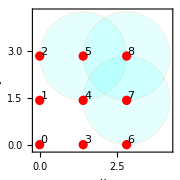

```mathematica
PlotAtoms[RydbergHub[UnitLattice->Sqrt[2]],ShowBlockade->{5,7,8},ImageSize->Small,LabelStyle->"Section"]
```

[Native gates]

 Init, Wait, Read, M, SRot, H, Rx[θ], Ry[θ], Rz[θ], SWAPLoc, ShiftLoc, CZ_(q1,q2,...),C[Z[θ]], C[Z]

## Arbitrary single rotation

Hadamard: ϕ→0,Δ→Ω,t→π/Ω̃

```mathematica
Ω=OptionValue[RydbergHub,RabiFreq]
```

0.1

```mathematica
CalcCircuitMatrix[Subscript[SRot, 0][0,Ω,π/Sqrt[2 Ω^2]]/.RydbergHub[][Aliases]]//Chop//MatrixForm
```

(0.-0.707107 ⅈ | 0.-0.707107 ⅈ
0.-0.707107 ⅈ | 0.+0.707107 ⅈ)

Rotation around x-axis  via  SRot[ϕ→0,Δ→0,t→θ/Ω ] or directly using Rx[θ]

```mathematica
InsertCircuitNoise[{Subscript[H, 0],Subscript[Rx, 0][π/Ω]},RydbergHub[]]
```

{{0,{H_0,Deph_0[2.5×10^-8]},{Depol_0[0.],Deph_0[0.],Depol_1[2.12057×10^-6],Deph_1[1.5708×10^-7],Depol_2[2.12057×10^-6],Deph_2[1.5708×10^-7],Depol_3[2.12057×10^-6],Deph_3[1.5708×10^-7],Depol_4[2.12057×10^-6],Deph_4[1.5708×10^-7],Depol_5[2.12057×10^-6],Deph_5[1.5708×10^-7],Depol_6[2.12057×10^-6],Deph_6[1.5708×10^-7],Depol_7[2.12057×10^-6],Deph_7[1.5708×10^-7],Depol_8[2.12057×10^-6],Deph_8[1.5708×10^-7]}},{31.4159,{Rx_0[31.4159],Deph_0[2.5×10^-7]},{Depol_0[0.],Deph_0[0.],Depol_1[0.0000212055],Deph_1[1.57079×10^-6],Depol_2[0.0000212055],Deph_2[1.57079×10^-6],Depol_3[0.0000212055],Deph_3[1.57079×10^-6],Depol_4[0.0000212055],Deph_4[1.57079×10^-6],Depol_5[0.0000212055],Deph_5[1.57079×10^-6],Depol_6[0.0000212055],Deph_6[1.57079×10^-6],Depol_7[0.0000212055],Deph_7[1.57079×10^-6],Depol_8[0.0000212055],Deph_8[1.57079×10^-6]}}}

## Multi-qubit gates

The operation controlled-Z up to a single qubit phase ϕ : inside blockade vs outside blockade

```mathematica
CalcCircuitMatrix[Subscript[CZ, 0,1][ϕ]/.RydbergHub[][Aliases]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(ⅈ (-π+2 ϕ)))

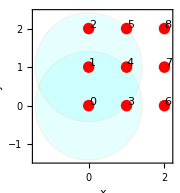

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{0,1},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[CZ, 0,1][ϕ]},RydbergHub[]]
```

{{0,{CZ_(0,1)[ϕ],KrausNonTP_(0,1)[{{{1,0,0,0},{0,0.9995,0,0},{0,0,0.9995,0},{0,0,0,0.9995}}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_2[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))],Depol_3[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_3[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))],Depol_4[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_4[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))],Depol_5[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_5[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))],Depol_6[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_6[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))],Depol_7[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_7[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))],Depol_8[0.75 (1-ⅇ^(-9.×10^-7 Abs[ϕ]))],Deph_8[0.5 (1-ⅇ^(-1.×10^-7 Abs[ϕ]))]}}}

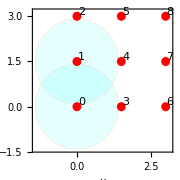

```mathematica
PlotAtoms[RydbergHub[UnitLattice->1.5],ShowBlockade->{0,1},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[CZ, 0,1][ϕ]},RydbergHub[UnitLattice->1.5]]
```

InsertCircuitNoise::error: Encountered gate CZ_(0,1)[ϕ] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

Multi-qubit gates C_cq__[Z_tq__] or C_cq__[Z_tq__,duration/Ω] , every qubit in cq and tq must be overlapping each other in the blockade radius

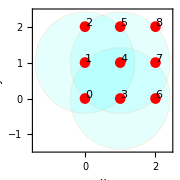

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{1,3,4},ImageSize->Small]
```

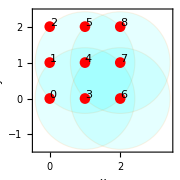

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{3,4,6,7},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[C, 4][Subscript[Z, 3,6,7][π√3]],Subscript[C, 4,5,7][Subscript[Z, 8][2π]],Subscript[C, 2,5][Subscript[Z, 4]]},RydbergHub[]];
```

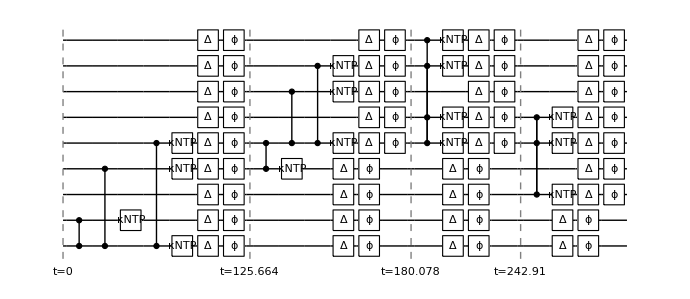

```mathematica
DrawCircuit@%
```

## Spatial operations

```mathematica
dev=RydbergHub[];
```

Shifting a bunch of qubits at once

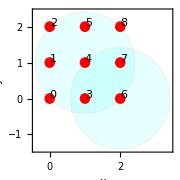

```mathematica
PlotAtoms[dev, ImageSize->Small,ShowBlockade->{4,6}]
```

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 0,1,2][{0,0.5}],Subscript[SWAPLoc, 8,7],Subscript[Wait, 0][.1],Subscript[ShiftLoc, 7,8,6][{0,-0.5}],Subscript[SWAPLoc, 4,6]},dev];
```

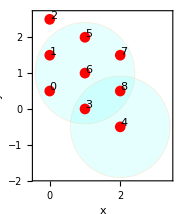

```mathematica
PlotAtoms[dev, ImageSize->Small,ShowBlockade->{4,6}]
```

## Scheduling : Rearrange circuit by parallel and serial

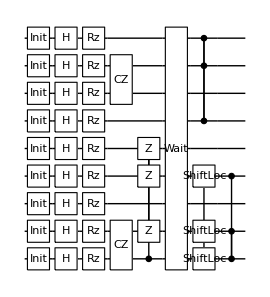

```mathematica
circ=Flatten@{{Subscript[Init, #],Subscript[H, #],Subscript[Rz, #][π/(#+1)]}&/@Range[0,8],Subscript[CZ, 6,7][π],Subscript[CZ, 0,1][π],Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[Wait, Range[0,8]][ϕ],Subscript[ShiftLoc, 0,1,3][{-1,0}],Subscript[C, 0,1][Subscript[Z, 3]],Subscript[C, 5,8][Subscript[Z, 7]]};
DrawCircuit@%
```

Parallel excution, where paralellism applies when the operations are done within non-overlaping blockade radii

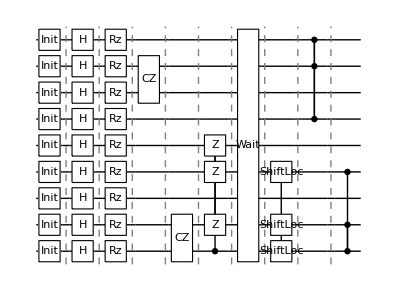

```mathematica
DrawCircuit@CircRydbergHub[circ,dev,Parallel->True]
```

Serial excution

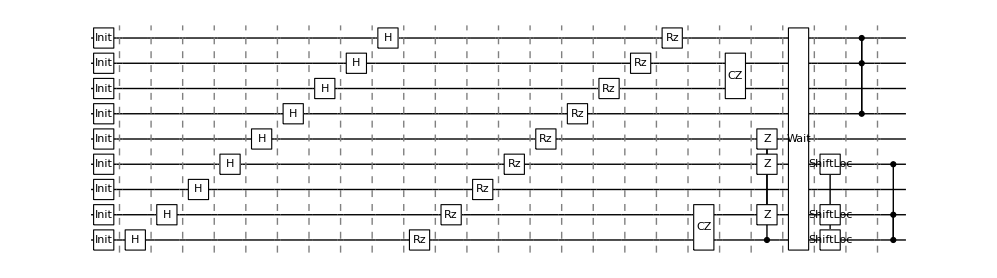

```mathematica
DrawCircuit@CircRydbergHub[circ,dev,Parallel->False]
```

Get noise-decorated circuit from rearranged circuit

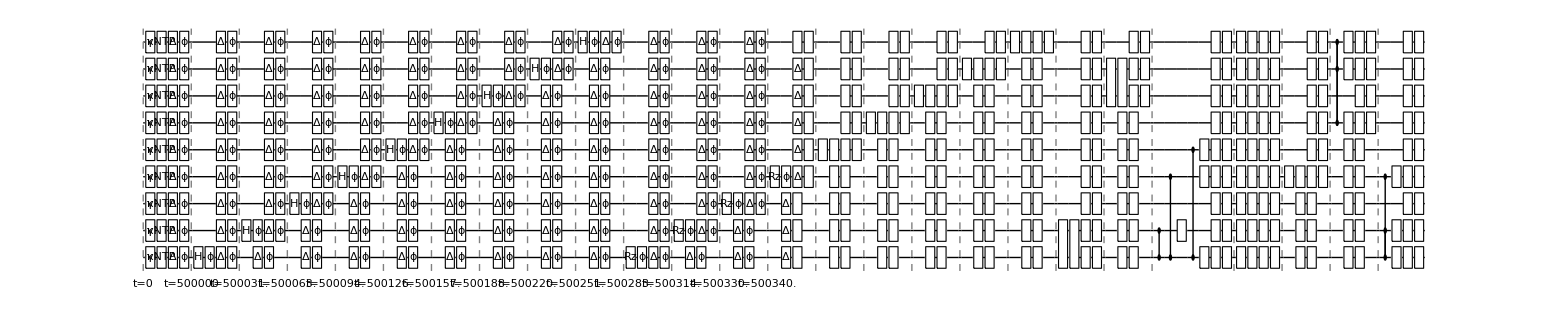

```mathematica
DrawCircuit@InsertCircuitNoise[CircRydbergHub[circ,dev,Parallel->False],dev]
```

## Quantum simulation: 9-GHZ

```mathematica
ghz={
Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],
Subscript[H, 0],
Subscript[H, 1],Subscript[H, 3],Subscript[H, 4], Subscript[C, 0][Subscript[Z, 1,3,4][3π]],Subscript[H, 1],Subscript[H, 3],Subscript[H, 4],
Subscript[H, 6],Subscript[H, 7],Subscript[C, 3][Subscript[Z, 6,7][π]],Subscript[H, 6],Subscript[H, 7],
Subscript[H, 5],Subscript[H, 8],Subscript[C, 7][Subscript[Z, 5,8]],Subscript[H, 5],Subscript[H, 8],
Subscript[H, 2],Subscript[C, 1][Subscript[Z, 2]],Subscript[H, 2]
};
```

```mathematica
(* allocate memory *)
ψ=CreateQureg[9];
ρ=CreateDensityQureg[9];
```

The non-native questlink gates are defined in the Aliases, so we need to replace those aliases into the native questlink gates. Apply the circuit in the state vector, noiseless case

```mathematica
ApplyCircuit[InitZeroState@ψ,Flatten[ghz/.dev[Aliases]]];
```

Initialise the qubits in a  random mixed state: extremely low fidelity

```mathematica
SetQuregMatrix[ρ,RandomMixState[9]];
CalcFidelity[ρ,ψ]
```

0.00206825

Then apply the circuit in serial manner

```mathematica
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[CircRydbergHub[ghz,dev,Parallel->False],dev]];
```

```mathematica
CalcFidelity[ρ,ψ]
```

0.907705